## Building ViennaRNA

Download release from GitHub: https://github.com/ViennaRNA/ViennaRNA?tab=readme-ov-file#installation

Build with something like this command:

./configure --prefix=/Users/christopher/Downloads/ViennaRNABuild/ --without-perl --without-python --without-swig --without-doc-html --without-doc-pdf --without-doc --enable-shared=yes --enable-static=no --enable-universal-binary=yes

make
make install

The --prefix is needed to install it in the right place. --without-perl is needed because of a dependency on EXTERN.h that doesn't work on my computer. --without-python and --without-swig are just paranoia. --without-doc (etc.) are because of weird file system problems with make install and the docs. --enable-shared, --enable-static, and --enable-universal-binary probably don't do anything.

This creates a static library (.a) which can then be wrapped in a dynamic library (.dylib) by making a dummy C file with irrelevant contents, and then running:

clang++ dummy.c --shared -Wl,-force_load,libRNA.a -o libwrapper.dylib

This builds libwrapper.dylib, which can then be loaded with FFI functions.

For me, dummy.c only contains:

void dummy() {}

(It might be possible to use an empty file, but I didn't check!)

## Init

C examples can be found in the examples directory on GitHub, or here: https://www.tbi.univie.ac.at/RNA/ViennaRNA/refman/examples/c.html

This has links for function signatures: https://gensoft.pasteur.fr/docs/ViennaRNA/2.4.14/examples_c.html

The path to the wrapper library built above:

```mathematica
$LibRNA=FileNameJoin[{NotebookDirectory[],"libwrapper.dylib"}]
```

/Users/christopher/Library/CloudStorage/Dropbox/mathematica/viennaRNA/libwrapper.dylib

## Basic

### FFI

Load the C functions needed for the simple example:

```mathematica
vrnaAllocC=ForeignFunctionLoad[$LibRNA,"vrna_alloc",{"CUnsignedInt"}->"OpaqueRawPointer"]
```

ForeignFunction[…]

```mathematica
vrnaFreeC=ForeignFunctionLoad[$LibRNA,"free",{"OpaqueRawPointer"}->"Void"]
```

ForeignFunction[…]

```mathematica
vrnaFoldC=ForeignFunctionLoad[$LibRNA,"vrna_fold",{"RawPointer"::["UnsignedInteger8"],"RawPointer"::["UnsignedInteger8"]}->"CFloat"]
```

ForeignFunction[…]

### Wrapper

Make some wrapper functions for convenience:

```mathematica
vrnaAlloc[len_]:=CreateManagedObject[vrnaAllocC[len],vrnaFreeC]
```

Bracket notation: https://gensoft.pasteur.fr/docs/ViennaRNA/2.4.14/rna_structure_notations.html#:~:text=The%20standard%20representation%20of%20a,bases%20are%20shown%20as%20dots.

```mathematica
vrnaFold[seq_]:=
Module[{structure,mfe,structureString},
structure=RawPointer[vrnaAlloc[StringLength[seq]+1],"UnsignedInteger8"];
mfe=vrnaFoldC[seq,structure];
structureString=RawMemoryImport[structure,"String"];
<|
"MinimumFreeEnergy"->Quantity[mfe,"ThermochemicalKilocalories"/"Moles"],
"Structure"->structureString,
"BioSequence"->BioSequence["RNA",seq,structureString]
|>
]
```

```mathematica
vrnaFold[seq_?(BioSequenceQ[#,"RNA"]&)]:=vrnaFold[seq["SequenceString"]]
```

```mathematica
RNAFold[seq_?(BioSequenceQ[#,"RNA"]&)]:=vrnaFold[seq["SequenceString"]]["BioSequence"]
```

```mathematica
RNAFoldMinimumFreeEnergy[seq_?(BioSequenceQ[#,"RNA"]&)]:=vrnaFold[seq["SequenceString"]]["MinimumFreeEnergy"]
```

### Examples

Fold a sequence:

```mathematica
seq=BioSequence["RNA","GAGUAGUGGAACCAGGCUAUGUUUGUGACUCGCAGACUAACA"]
```

BioSequence[…]

Plot it:

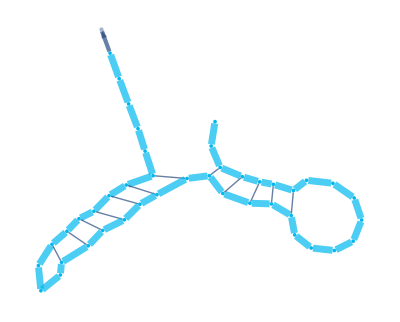

```mathematica
BioSequencePlot[RNAFold[seq]]
```

Fold some random sequences of length 100:

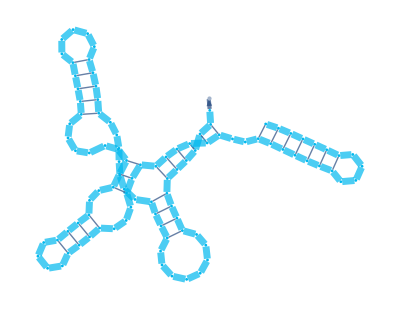
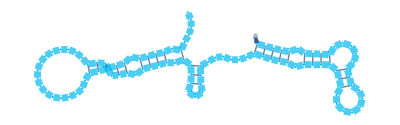
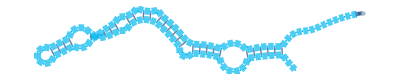
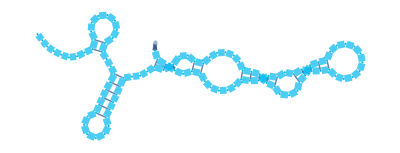
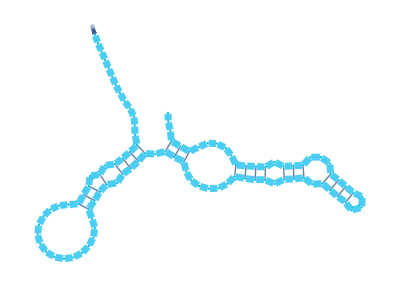
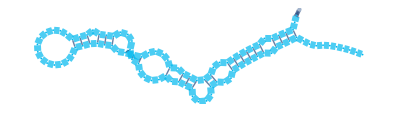
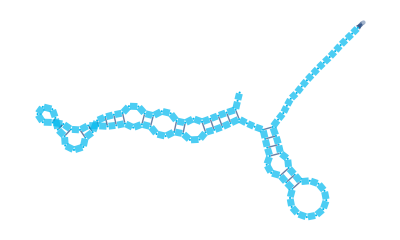
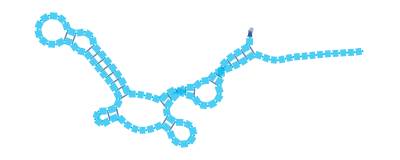

```mathematica
Table[BioSequencePlot@RNAFold@BioSequence["RNA",StringJoin@RandomChoice[{"G","U","A","C"},100]],10]
```

Fold a big RNA:

```mathematica
BioSequencePlot@RNAFold@BioSequence["RNA",StringJoin@RandomChoice[{"G","U","A","C"},1000]]
```

-Graphics-

### Runtime analysis

```mathematica
runtimesData=Table[{n,First@AbsoluteTiming@vrnaFold[StringJoin@RandomChoice[{"G","U","A","C"},n]]},{n,1,2001,100}];
```

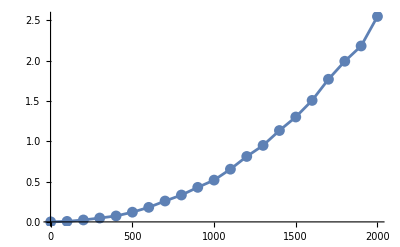

```mathematica
ListLinePlot[runtimesData,Mesh->All]
```

### Complements

```mathematica
seq=RNAFold[BioSequence["RNA",StringJoin@RandomChoice[{"G","U","A","C"},100]]]
```

BioSequence[…]

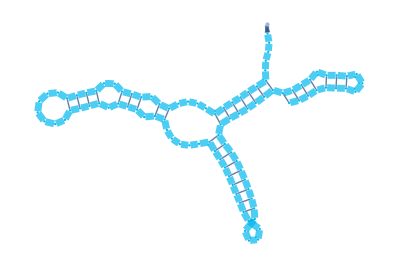

```mathematica
BioSequencePlot@seq
```

```mathematica
RNAFold[BioSequenceComplement[seq1]]
```

BioSequence[…]

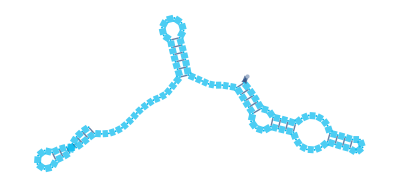

```mathematica
BioSequencePlot@RNAFold[BioSequenceComplement[seq1]]
```

### Lower level interface

```mathematica
vrnaFold["GAGUAGUGGAACCAGGCUAUGUUUGUGACUCGCAGACUAACA"]
```

<|MinimumFreeEnergy→-8.8 kcal_th/mol,Structure→..(((((........)))))(((((((...))))))).....,BioSequence→BioSequence[…]|>

## More general interface

### FFI

```mathematica
foldCompoundT="OpaqueRawPointer";
```

```mathematica
mdT="OpaqueRawPointer";
```

```mathematica
vrnaAllocC=ForeignFunctionLoad[$LibRNA,"vrna_alloc",{"CUnsignedInt"}->"OpaqueRawPointer"];
```

```mathematica
vrnaFreeC=ForeignFunctionLoad[$LibRNA,"free",{"OpaqueRawPointer"}->"Void"];
```

```mathematica
foldCompoundC=ForeignFunctionLoad[$LibRNA,"vrna_fold_compound",{"RawPointer"::["UnsignedInteger8"],mdT,"CUnsignedInt"}->foldCompoundT];
```

```mathematica
foldCompoundFreeC=ForeignFunctionLoad[$LibRNA,"vrna_fold_compound_free",{foldCompoundT}->"Void"];
```

```mathematica
mfeC=ForeignFunctionLoad[$LibRNA,"vrna_mfe",{foldCompoundT,"RawPointer"::["UnsignedInteger8"]}->"CFloat"];
```

```mathematica
expParamsRescaleC=ForeignFunctionLoad[$LibRNA,"vrna_exp_params_rescale",{foldCompoundT,"RawPointer"::["CDouble"]}->"Void"];
```

```mathematica
pfC=ForeignFunctionLoad[$LibRNA,"vrna_pf",{foldCompoundT,"RawPointer"::["UnsignedInteger8"]}->"CFloat"];
```

```mathematica
centroidC=ForeignFunctionLoad[$LibRNA,"vrna_centroid",{foldCompoundT,"RawPointer"::["CDouble"]}->"RawPointer"::["UnsignedInteger8"]];
```

### Wrapper

```mathematica
vrnaAlloc[len_]:=CreateManagedObject[vrnaAllocC[len],vrnaFreeC]
```

```mathematica
foldCompound[seq_,md_,options_]:=CreateManagedObject[foldCompoundC[seq,md,options],foldCompoundFreeC]
```

### Examples

```mathematica
seq="GAGUAGUGGAACCAGGCUAUGUUUGUGACUCGCAGACUAACA";
```

```mathematica
vc=foldCompound[seq,OpaqueRawPointer[0],0];
```

```mathematica
structure=RawPointer[vrnaAlloc[StringLength[seq]+1],"UnsignedInteger8"];
```

```mathematica
mfe=mfeC[vc,structure]
```

-8.8

```mathematica
RawMemoryImport[structure,"String"]
```

..(((((........)))))(((((((...))))))).....

```mathematica
BioSequence["RNA",seq,RawMemoryImport[structure,"String"]]
```

BioSequence[…]

```mathematica
mfePtr=RawMemoryExport[mfe,"CDouble"];
```

```mathematica
expParamsRescaleC[vc,mfePtr]
```

```mathematica
RawMemoryRead[mfePtr]
```

-8.8

```mathematica
probStrPtr=RawPointer[vrnaAlloc[StringLength[seq]+1],"UnsignedInteger8"];
```

```mathematica
en=pfC[vc,probStrPtr]
```

13805.5

```mathematica
RawMemoryImport[probStrPtr,"String"]
```

..(((((........)))))(((((((...))))))).....

```mathematica
distPtr=RawMemoryAllocate["CDouble"];
```

```mathematica
cent=centroidC[vc,distPtr]
```

RawPointer[…]

```mathematica
RawMemoryRead[distPtr]
```

1.21858

```mathematica
RawMemoryImport[cent,"String"]
```

..(((((........)))))(((((((...))))))).....

## Scratch space

```mathematica
$LibRNA="/Users/christopher/Downloads/ViennaRNABuild/lib/libwrapper.dylib";
```

```mathematica
ForeignPointerLookup["/Users/christopher/Downloads/ViennaRNABuild/lib/libwrapper.dylib","vrna_alloc"]
```

OpaqueRawPointer[…]

```mathematica
vrnaAllocC=ForeignFunctionLoad[$LibRNA,"vrna_alloc",{"CUnsignedInt"}->"OpaqueRawPointer"]
```

ForeignFunction[…]

```mathematica
vrnaFoldC=ForeignFunctionLoad[$LibRNA,"vrna_fold",{"RawPointer"::["UnsignedInteger8"],"RawPointer"::["UnsignedInteger8"]}->"CFloat"]
```

ForeignFunction[…]

```mathematica
seq="GAGUAGUGGAACCAGGCUAUGUUUGUGACUCGCAGACUAACA";
```

```mathematica
structurePtr=vrnaAllocC[StringLength[seq]+1]
```

OpaqueRawPointer[…]

```mathematica
vrnaFoldC[seq,structurePtr]
```

-8.8

```mathematica
RawMemoryImport[RawPointer[structurePtr,"RawPointer"::["UnsignedInteger8"]],"String"]
```

..(((((........)))))(((((((...))))))).....

```mathematica
parenPairings[str_]:=
With[{c=Characters[str]},
Reap[Fold[
Switch[#2[[2]],
"(",Append[#1,#2[[1]]],
")",Sow[{Last[#1],#2[[1]]}];Most[#1],
_,#1
]&,
{},
Transpose[{Range@Length@c,c}]
]][[2,1]]
]
```

```mathematica
Sort@parenPairings["..(((((........)))))(((((((...)))))))....."]
```

{{3,20},{4,19},{5,18},{6,17},{7,16},{21,37},{22,36},{23,35},{24,34},{25,33},{26,32},{27,31}}